# Homework 6

## Question 3

```mathematica
n=3;
p = 1/(2^n * n!)*D[(x^2-1)^n,{x,n}];
Simplify[p]

(2n+1)/(2)Integrate[x*p,{x,0,1}]
Simplify[(2n+1)/(2)Integrate[x*p,{x,0,1}]*p]
```

1/2 x (-3+5 x^2)

0

0

Piecewise[{{0, x<0}, {x, x<1}, {0, True}}]

1/4

x/2

5/32 (-1+3 x^2)

-3/256 (3-30 x^2+35 x^4)

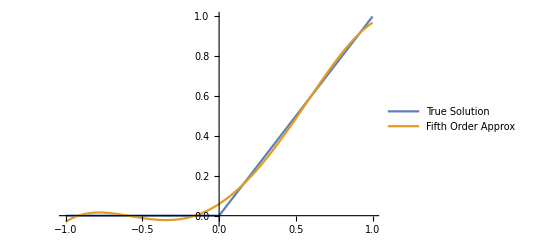

```mathematica
Subscript[f, true][x_] = Piecewise[{{0,x<0},{x,x<1}}]

Subscript[f, 0][x_] = 1/4
Subscript[f, 1][x_] = 1/2 * x
Subscript[f, 2][x_] = 5/32 (-1+3 x^2)
Subscript[f, 4][x_] = -3/256 (3-30 x^2+35 x^4)
Plot[{Subscript[f, true][x],Subscript[f, 0][x]+Subscript[f, 1][x]+Subscript[f, 2][x]+Subscript[f, 4][x]},{x,-1,1},PlotLegends->{"True Solution","Fifth Order Approx"}]
```